8.58

1

-0.89

2.15

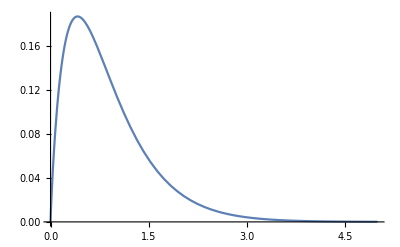

(a1 ⅇ^(-b1 p))/(b1 p)-(a2 ⅇ^(-b2 p))/(b2 p)

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1→5.23391,a2→6.36994,b1→1.54508,b2→1.77652}

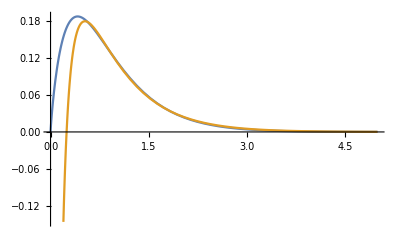

```mathematica
Clear[R0,alpha,b,p,y,a1,a2,b1,b2, alp,bet, w,t,s]

R0=8.58
a=1
alp = -0.89
bet = 2.15
w[p_,alpha_,b_] = Exp[-b*p]/(p/a)^(alpha);                                                                        (* tempered Riesz FC *)
data = Table[{x,w[x,alp,bet]},{x,0.5,6,0.01}];
Plot[w[x,alp,bet],{x,0,5}]

y[ p_, a1_,a2_,b1_,b2_] =a1 *Exp[-b1*p]/(b1*p)- a2 *Exp[-b2*p]/(b2*p); 
t = a1 *Exp[-b1*p]/(b1*p)- a2 *Exp[-b2*p]/(b2*p) 
s= FindFit[data,y[p,a1,a2,b1,b2],{a1,a2,b1,b2},p]
Plot[{w[p,alp,bet],t /. s},{p,0, 5}]
```